# 1D Linear chain with s, p orbital

Authors
Affiliation
Date of submission

Here we are going to solve the electronic structure for 1D linear chain with 1 atom in the unit cell with only s orbital.

## The wavefunction of the linear chain with 1 atom per Unit Cell either with s or p orbital

For s orbital of the atomic orbital

```mathematica
Subscript[χ, s][x_,k_]:=Sum[Exp[ⅈ k i a0] Exp[-5 Abs[x-i a0]],{i,-20,20}]; (*wave function Xs*)
```

For p orbital:

```mathematica
Subscript[χ, p][x_,k_]:=Sum[Exp[ⅈ k i a0] 20 (x-i a0)  Exp[-10 Abs[x-i a0]],{i,-20,20}];
```

```mathematica
pts=Table[{a0 i,0},{i,-20,20}];
```

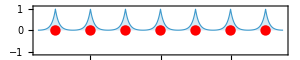
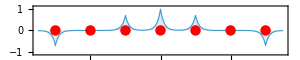
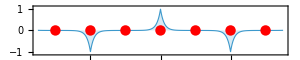
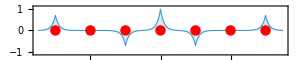
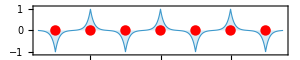

```mathematica
a0=2;
Table[Plot[Subscript[χ, s][x,(k π)/a0]//Re, {x,-7,7},
Epilog->{PointSize[0.025],Red,Point[pts]},
PlotRange->{-1.1,1.1},
Frame->True,
FrameTicks->None,
ImageSize->300,
AspectRatio->0.2,
Filling->Axis,
PlotStyle->AbsoluteThickness[0.8],
PlotLabel->k
],{k,{0.,1/4,1/2,3/4,1}}]
```

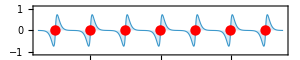
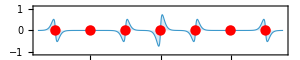
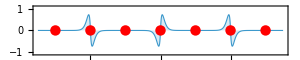
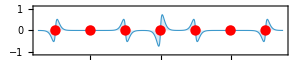
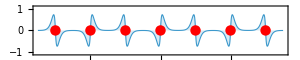

```mathematica
Table[Plot[Subscript[χ, p][x,(k π)/a0]//Re, {x,-7,7},
Epilog->{PointSize[0.025],Red,Point[pts]},
PlotRange->{-1.1,1.1},
Frame->True,
FrameTicks->None,
ImageSize->300,
AspectRatio->0.2,
Filling->Axis,
PlotStyle->AbsoluteThickness[0.8],
PlotLabel->k
],{k,{0.,1/4,1/2,3/4,1}}]
```

What is the band structure of this system?

## The band structure for the 1 D chain only with 1 atom per unit cell and s orbital or p orbitals.

The result has Cos(k a) , since we are going to plot along k scaled to π/a, then k will take values from -1 to 1; then k a becomes k π/a a=k π

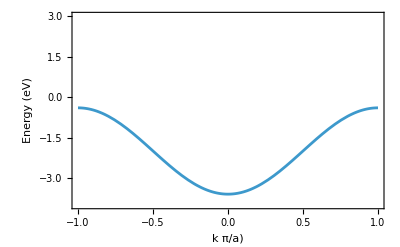

```mathematica
Plot[es + 2 ts Cos[π k]/.{es->-2,ts->-0.8}//Evaluate,{k,-1,1},
PlotRange->{{-1,1},{-4,3}},
Frame->True,
FrameLabel->{"k π/a)","Energy (eV)"},
Axes->False
]
```

```mathematica
Manipulate[Plot[es + 2 ts Cos[π k]/.{es->-2}//Evaluate,{k,-1,1},
PlotRange->{{-1,1},{-4,3}},
Frame->True,
FrameLabel->{"k π/a)","Energy (eV)"},
Axes->False
],{{ts, -0.8},-2,2}]
```

For the case of the p orbitals

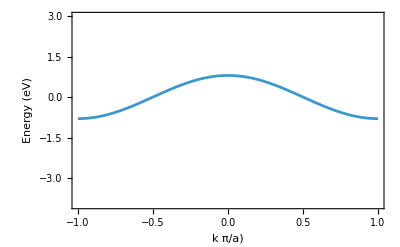

```mathematica
Plot[ep 2 tp Cos[π k]/.{ep->0.5,tp->0.8}//Evaluate,{k,-1,1},
PlotRange->{{-1,1},{-4,3}},
Frame->True,
FrameLabel->{"k π/a)","Energy (eV)"},
Axes->False
]
```

```mathematica
Manipulate[Plot[ep + 2 tp Cos[π k]/.{ep->0.5}//Evaluate,{k,-1,1},
PlotRange->{{-1,1},{-4,3}},
Frame->True,
FrameLabel->{"k π/a)","Energy (eV)"},
Axes->False
],{{tp, -0.8},-2,2}]
```

## The band structure for a 1 D chain with 1 atom with s a & px orbitals.

```mathematica
H ={{es + ts (Exp[-ⅈ k a]+Exp[ⅈ k a]),tsp (Exp[-ⅈ k a]-Exp[ⅈ k a])},
{tsp  (Exp[ⅈ k a]-Exp[-ⅈ k a]),ep + tp (Exp[-ⅈ k a]+Exp[ⅈ k a])}

}//FullSimplify;
```

```mathematica
H//MatrixForm
```

(es+2 ts Cos[a k] | -2 ⅈ tsp Sin[a k]
2 ⅈ tsp Sin[a k] | ep+2 tp Cos[a k])

```mathematica
eigenval = (Eigenvalues[H]//FullSimplify)//PowerExpand;
eigenval//TableForm
```

1/2 (ep+es+2 (tp+ts) Cos[a k]-√((ep-es)^2+2 (tp-ts)^2+8 tsp^2+4 (ep-es) (tp-ts) Cos[a k]+2 ((tp-ts)^2-4 tsp^2) Cos[2 a k]))
1/2 (ep+es+2 (tp+ts) Cos[a k]+√((ep-es)^2+2 (tp-ts)^2+8 tsp^2+4 (ep-es) (tp-ts) Cos[a k]+2 ((tp-ts)^2-4 tsp^2) Cos[2 a k]))

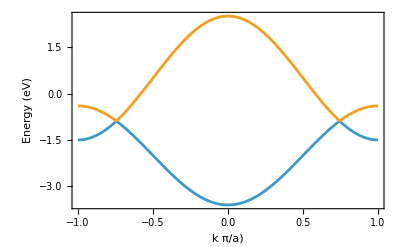

```mathematica
Plot[eigenval/.{a->π, es->-2, ep->0.5, ts->-0.8,tp->1, tsp->0}//Evaluate,{k,-1,1},
Frame->True,
FrameLabel->{"k π/a)","Energy (eV)"},
Axes->False
 ]
```

The obove plot is when we do not have s and p interaction

```mathematica
Manipulate[Plot[eigenval/.{a->π, es->-2, ep->0.5, ts->-0.8,tp->1, tsp->val}//Evaluate,{k,-1,1},
Frame->True,
FrameLabel->{"k (π/a)","Energy (eV)"},
Axes->False
 ],
{{val,0,"t_sp"},-1,1}
]
```

The above plot is when we allow the interaction between the s and p orbital

## The band structure for a 1 D chain with 1 atom with s and px & py orbitals

```mathematica
H ={{es + ts (Exp[-ⅈ k a]+Exp[ⅈ k a]),tsp (Exp[-ⅈ k a]-Exp[ⅈ k a])},
{tsp  (Exp[ⅈ k a]-Exp[-ⅈ k a]),ep + tp (Exp[-ⅈ k a]+Exp[ⅈ k a])}

}//FullSimplify;
```

```mathematica
H//MatrixForm
```

(es+2 ts Cos[a k] | -2 ⅈ tsp Sin[a k]
2 ⅈ tsp Sin[a k] | ep+2 tp Cos[a k])

```mathematica
eigenval = (Eigenvalues[H]//FullSimplify)//PowerExpand;
eigenval//TableForm
```

1/2 (ep+es+2 (tp+ts) Cos[a k]-√((ep-es)^2+2 (tp-ts)^2+8 tsp^2+4 (ep-es) (tp-ts) Cos[a k]+2 ((tp-ts)^2-4 tsp^2) Cos[2 a k]))
1/2 (ep+es+2 (tp+ts) Cos[a k]+√((ep-es)^2+2 (tp-ts)^2+8 tsp^2+4 (ep-es) (tp-ts) Cos[a k]+2 ((tp-ts)^2-4 tsp^2) Cos[2 a k]))

```mathematica
Plot[eigenval/.{a->π, es->-2, ep->0.5, ts->-0.8,tp->1, tsp->0}//Evaluate,{k,-1,1},
Frame->True,
FrameLabel->{"k π/a)","Energy (eV)"},
Axes->False
 ]
```

-Graphics-

```mathematica
Manipulate[Plot[eigenval/.{a->π, es->-2, ep->0.5, ts->tsval,tp->tpσval, tsp->tspval}//Evaluate,{k,-1,1},
Frame->True,
FrameLabel->{"k (π/a)","Energy (eV)"},
Axes->False
 ],
{{tsval,-0.8,"t_s"},-2,0},
{{tpσval,1,"t_pσ"},0,2},
{{tspval,0,"t_sp"},-2,0}
]
```

### The band structure for 1 D chain with 1 atom per unit cell with s, p_x & p_y orbitals.

Please notice that H is  a 3x3 matrix, then the electronic structure will have 3 bands.